# Chaos Game

### Author

Eric W. Weisstein
February 7, 2011

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Fractals/ChaosGame.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/ChaosGame.html.

For a list of Eric's math packages that may be needed to evaluate this notebook, see Mathematica Information Center's MathSource item 4775.  A list of Eric's utility packages that may be needed to evaluate this notebook may be downloaded from MathSource item 5087.

©2011 Wolfram Research, Inc. except for portions noted otherwise

### Initialization

```mathematica
<<MathWorld`Fractal`
```

### Usage

```mathematica
?ChaosGame
```

ChaosGame[n,its,drop] gives its iterations of the chaos game on an n-gon with its points using a ratio of 1/2, dropping the  first drop points.  ChaosGame[{n.r},its,drop] uses a ratio r.

## Plots

```mathematica
<<Utilities`Typesetting`
```

```mathematica
MakeBoxes[label[n_,Rational[a_,b_]],TraditionalForm]:=RowBox[{RowBox[{"n","==",n}],",",RowBox[{"r","==",MakeBoxes[InlineFraction[a,b],TraditionalForm]}]}]
```

#### V5

```mathematica
Show[GraphicsArray[Partition[Graphics[{PointSize[.005],Point/@ChaosGame[#,20000]},
AspectRatio->Automatic,
PlotLabel->TraditionalForm[label@@#]
]&/@{
{3,1/2},
{5,1/3},
{5,3/8},
{6,1/3}
},2]]]
```

⁃GraphicsArray⁃

```mathematica
Show[GraphicsArray[Partition[Table[Graphics[{PointSize[.005],Point/@ChaosGame[i,30000]},
AspectRatio->Automatic
],{i,3,6}],2]]]
```

⁃GraphicsArray⁃

```mathematica
Show[GraphicsArray[Partition[Graphics[{PointSize[.005],Point/@ChaosGame[{4,#},20000]},AspectRatio->Automatic]&/@{0.25,0.4,0.5,0.6,0.75, 0.9},3]]]
```

⁃GraphicsArray⁃

#### V6

```mathematica
MakeBoxes[label[n_,Rational[a_,b_]],TraditionalForm]:=RowBox[{"n","==",MakeBoxes[n,TraditionalForm],",","r","==",MakeBoxes[a,TraditionalForm],"/",MakeBoxes[b,TraditionalForm]}]
```

```mathematica
MakeBoxes[label[Rational[a_,b_]],TraditionalForm]:=RowBox[{"r","==",MakeBoxes[a,TraditionalForm],"/",MakeBoxes[b,TraditionalForm]}]
```

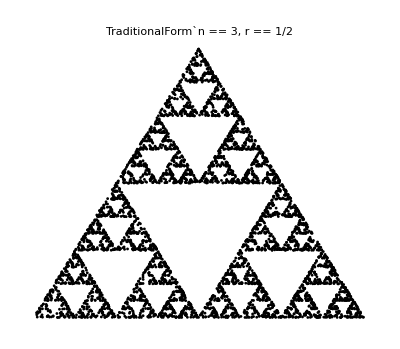
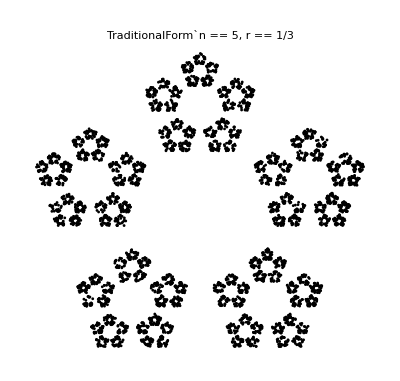
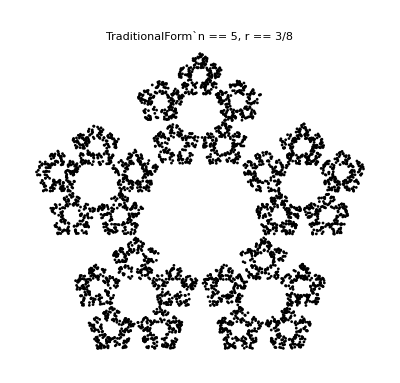

```mathematica
g1=Graphics[{PointSize[.005],Point[ChaosGame[#,5000]]},
PlotLabel->Style[ToString[label@@#,TraditionalForm],ShowStringCharacters->False]
]&/@{{3,1/2},{5,1/3},{5,3/8}
}
```

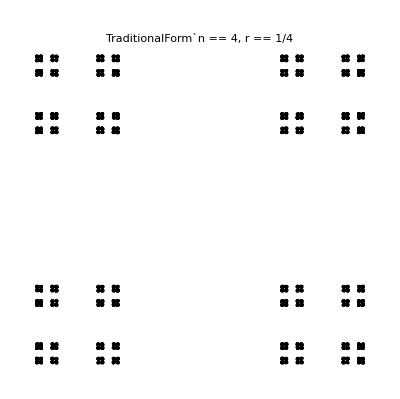
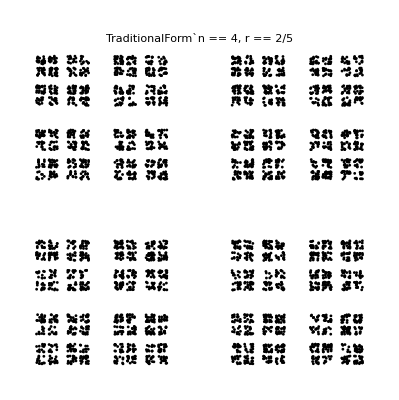
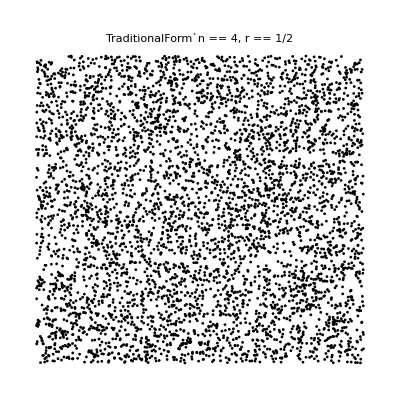

```mathematica
g2=Graphics[{PointSize[.005],Point[ChaosGame[{4,#},5000]]},PlotLabel->Style[ToString[label[4,#],TraditionalForm],ShowStringCharacters->False]]&/@{1/4,2/5,1/2}
```

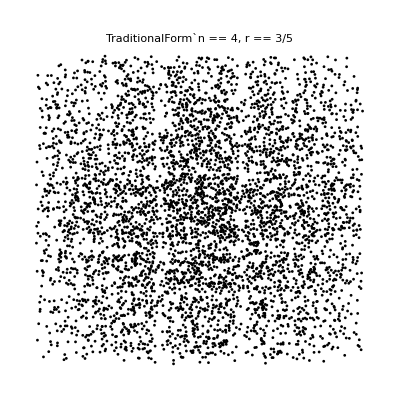
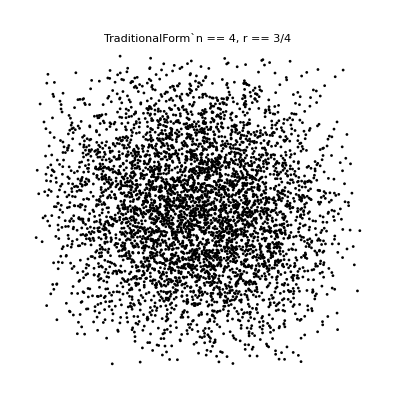
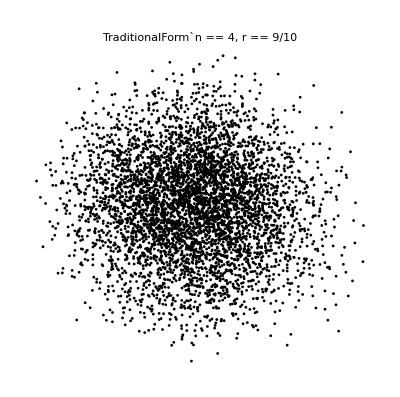

```mathematica
g3=Graphics[{PointSize[.005],Point[ChaosGame[{4,#},5000]]},PlotLabel->Style[ToString[label[4,#],TraditionalForm],ShowStringCharacters->False]]&/@{3/5,3/4,9/10}
```

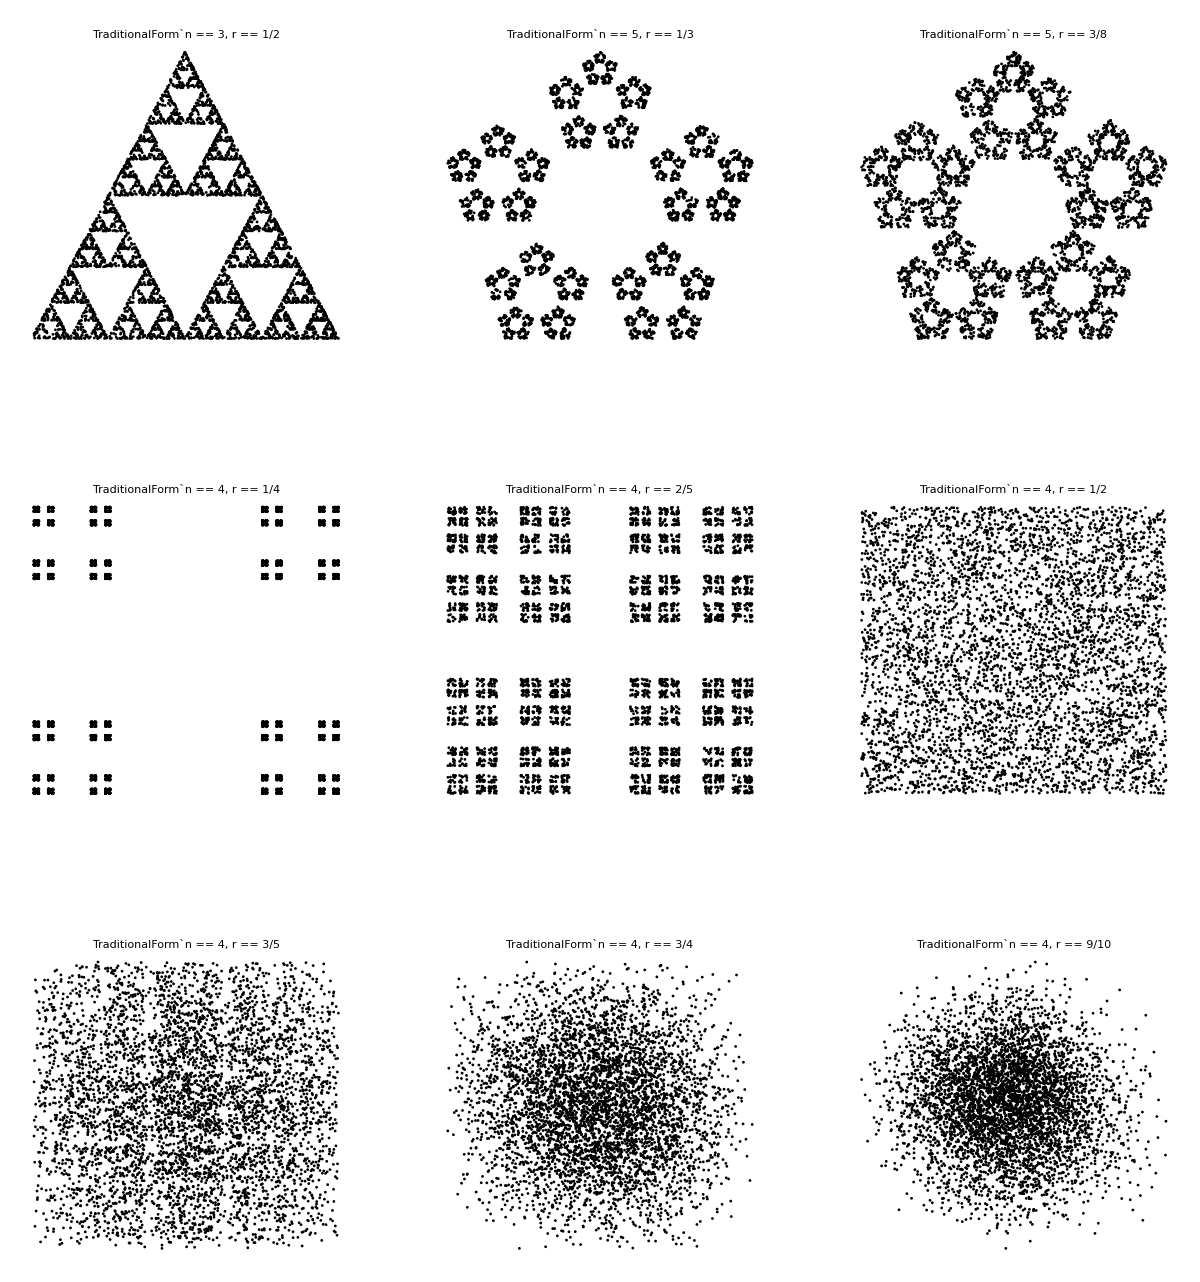

```mathematica
GraphicsGrid[{g1,g2,g3},Spacings->{40,80}]
```

## Animation

```mathematica
ChaosGame[{n_Integer?Positive,r_},pts_:1000,drop_:10]:=Module[{v,x0=0.,y0=0.,sc=1.,p,i,p0},p0=2Random[Integer,{1,n}]{x0,y0};
v=Table[{x0,y0}+sc{Cos[Pi/2+2 Pi i/n],Sin[Pi/2+2 Pi i/n]},{i,0,n-1}];
p=NestList[r Plus[#,v[[Random[Integer,{1,n}]]]]&,p0,pts];
Drop[p,drop]]
```

```mathematica
ChaosGame[{5,1/3},3,0]
```

{{0.,0.},{0.195928,-0.269672},{-0.130619,-0.359563},{0.152389,-0.389527}}

```mathematica
ChaosGameAnimation[{n_Integer?Positive,r_},pts_:10]:=Module[{nf=},
Graphics[{
{PointSize[.02],Red,Point[Through[{Cos,Sin}[Pi/2+2 Pi #/n]]&/@Range[0,n-1]]},
MapIndexed[Text[#2[[1]],.03{1,1}+#1]&,#],Point[#]}]&/@Reverse[NestList[Most,ChaosGame[{n,r},pts,0],pts]]
]
```

```mathematica
ListAnimate[ChaosGameAnimation[{5,1/3},10]]
```

```mathematica
Reverse[NestList[Most,Range[5],5]]
```

{{},{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}